```mathematica
Needs["MagneticKP`"];
```

## Core module

#### The input of kpHam function

```mathematica
input=<|"Unitary"->
<|C3->{-IdentityMatrix[4]/2+I √3 KroneckerProduct[PauliMatrix[3],PauliMatrix[2]]/2,{-kx/2-(√3 ky)/2,(√3 kx)/2-ky/2,kz}},C2->{KroneckerProduct[PauliMatrix[0],PauliMatrix[3]],{-kx,ky,-kz}},σh->{KroneckerProduct[PauliMatrix[3],PauliMatrix[0]],{kx,ky,-kz}}|>,"Anitunitary"-><|IT->{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky,kz}}|>|>
```

<|Unitary→<|C3→{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,-1/2,-(√3)/2},{0,0,(√3)/2,-1/2}},{-kx/2-(√3 ky)/2,(√3 kx)/2-ky/2,kz}},C2→{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{-kx,ky,-kz}},σh→{{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{kx,ky,-kz}}|>,Anitunitary→<|IT→{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky,kz}}|>|>

#### Generate the 1-st order kp Hamiltonian. Default method is Iterative Simplification Algorithm.

```mathematica
kpHam[1,input]["ham"]//MatrixForm
```

(C_(0,1)+C_(0,2)-ky C_(1,1)-ky C_(1,2) | kx C_(1,1)+kx C_(1,2) | 0 | kz C_(1,3)
kx C_(1,1)+kx C_(1,2) | C_(0,1)+C_(0,2)+ky C_(1,1)+ky C_(1,2) | kz C_(1,3) | 0
0 | kz C_(1,3) | C_(0,1)-C_(0,2)+ky C_(1,1)-ky C_(1,2) | kx C_(1,1)-kx C_(1,2)
kz C_(1,3) | 0 | kx C_(1,1)-kx C_(1,2) | C_(0,1)-C_(0,2)-ky C_(1,1)+ky C_(1,2))

#### Use Direct-Product Decomposition Algorithm

```mathematica
kpHam[1,input,"Method"->"DirectProductDecomposition"]["ham"]//MatrixForm
```

(C_(0,1)+C_(0,2)-ky C_(1,1)-ky C_(1,2) | kx C_(1,1)+kx C_(1,2) | 0 | -kz C_(1,3)
kx C_(1,1)+kx C_(1,2) | C_(0,1)+C_(0,2)+ky C_(1,1)+ky C_(1,2) | -kz C_(1,3) | 0
0 | -kz C_(1,3) | C_(0,1)-C_(0,2)-ky C_(1,1)+ky C_(1,2) | -kx C_(1,1)+kx C_(1,2)
-kz C_(1,3) | 0 | -kx C_(1,1)+kx C_(1,2) | C_(0,1)-C_(0,2)+ky C_(1,1)-ky C_(1,2))

#### Generate the 2-nd order kp Hamiltonian

```mathematica
kpHam[2,input]
```

<|ham→{{C_(0,1)+C_(0,2)-ky C_(1,1)-ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(kx^2-ky^2) C_(2,2)+(kx^2+ky^2) C_(2,3)+(kx^2-ky^2) C_(2,4)+kz^2 C_(2,6)+kz^2 C_(2,7),kx C_(1,1)+kx C_(1,2)-2 kx ky C_(2,2)-2 kx ky C_(2,4),kx kz C_(2,5),kz C_(1,3)-ky kz C_(2,5)},{kx C_(1,1)+kx C_(1,2)-2 kx ky C_(2,2)-2 kx ky C_(2,4),C_(0,1)+C_(0,2)+ky C_(1,1)+ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(-kx^2+ky^2) C_(2,2)+(kx^2+ky^2) C_(2,3)+(-kx^2+ky^2) C_(2,4)+kz^2 C_(2,6)+kz^2 C_(2,7),kz C_(1,3)+ky kz C_(2,5),kx kz C_(2,5)},{kx kz C_(2,5),kz C_(1,3)+ky kz C_(2,5),C_(0,1)-C_(0,2)+ky C_(1,1)-ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(kx^2-ky^2) C_(2,2)+(-kx^2-ky^2) C_(2,3)+(-kx^2+ky^2) C_(2,4)+kz^2 C_(2,6)-kz^2 C_(2,7),kx C_(1,1)-kx C_(1,2)+2 kx ky C_(2,2)-2 kx ky C_(2,4)},{kz C_(1,3)-ky kz C_(2,5),kx kz C_(2,5),kx C_(1,1)-kx C_(1,2)+2 kx ky C_(2,2)-2 kx ky C_(2,4),C_(0,1)-C_(0,2)-ky C_(1,1)+ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(-kx^2+ky^2) C_(2,2)+(-kx^2-ky^2) C_(2,3)+(kx^2-ky^2) C_(2,4)+kz^2 C_(2,6)-kz^2 C_(2,7)}},korder→{0,1,2},dim→4,NumberOfParameters→12|>

## Interface with SpaceGroupIrep package

```mathematica
Needs["SpaceGroupIrep`"];
```

```mathematica
showLGCharTab[24,"W"]
```

No.24 I2_12_12_1:  k-point name is W
BC standard:

  k_BC=(,,3/4-1/4-1/4) for ,,OrthBody(a)OrthBody(b)OrthBody(c)
Index |  |  |  | 1 | 2 | 3 | 4
Element |  |  |  | {E|000} | {C_(2x)|01/21/2} | {C_(2y)|1/21/20} | {C_(2z)|1/201/2}
Rotation
matrix |  |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | -1 | 1
0 | -1 | 0
1 | -1 | 0) | (-1 | 0 | 0
-1 | 0 | 1
-1 | 1 | 0) | (0 | 1 | -1
1 | 0 | -1
0 | 0 | -1)
Spin(↓↑)
rotation
matrix |  |  |  | (1 | 0
0 | 1) | (0 | -ⅈ
-ⅈ | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ)
1 | W_1 | ^1F | x | 2 | 0 | 0 | 0
2 | W_2 | Ā | x | 1 | -ⅈ | ⅈ | ⅈ
3 | W_3 | (B̄)_1 | x | 1 | ⅈ | -ⅈ | ⅈ
4 | W_4 | (B̄)_2 | x | 1 | ⅈ | ⅈ | -ⅈ
5 | W_5 | (B̄)_3 | x | 1 | -ⅈ | -ⅈ | -ⅈ

```mathematica
input=interfaceRep[24,"W",1]
```

<|Unitary→<|{C_(2x)|01/21/2}→{{{0,ⅈ},{-ⅈ,0}},{kx,-ky,-kz}},{C_(2y)|1/21/20}→{{{1,0},{0,-1}},{-kx,ky,-kz}}|>,Anitunitary→<||>,lable→{^1F,W_1}|>

```mathematica
kpHam[1,input]["ham"]//MatrixForm
```

(C_(0,1)+ky C_(1,2) | -ⅈ kx C_(1,1)+kz C_(1,3)
ⅈ kx C_(1,1)+kz C_(1,3) | C_(0,1)-ky C_(1,2))

```mathematica
input=interfaceRep[24,"W",1,"CartesianCoordinates"->True];
kpHam[1,input]["ham"]//MatrixForm
```

(C_(0,1)+ky C_(1,2) | -ⅈ kx C_(1,1)+kz C_(1,3)
ⅈ kx C_(1,1)+kz C_(1,3) | C_(0,1)-ky C_(1,2))

## Interface with MSGCorep package

```mathematica
Needs["MSGCorep`"];
```

```mathematica
showMLGCorep[{191,234},"K"]
```

MSG 191.234(P6/mmm1'):  k-point name is K, for ,,HexaPrim
▶  k=(,,-1/32/30) standard
Index |  |  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24
Element |  |  | {E|000} | {C_3^+|000} | {C_3^-|000} | {C''_21|000} | {C''_22|000} | {C''_23|000} | {S_3^-|000} | {σ_h|000} | {S_3^+|000} | {σ_d1|000} | {σ_d2|000} | {σ_d3|000} | {I|000}' | {C_6^+|000}' | {C_2|000}' | {C_6^-|000}' | {C'_21|000}' | {C'_22|000}' | {C'_23|000}' | {S_6^-|000}' | {S_6^+|000}' | {σ_v1|000}' | {σ_v2|000}' | {σ_v3|000}'
Rotation
matrix |  |  | (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1) | (0 | -1 | 0
1 | -1 | 0
0 | 0 | 1) | (-1 | 1 | 0
-1 | 0 | 0
0 | 0 | 1) | (1 | -1 | 0
0 | -1 | 0
0 | 0 | -1) | (-1 | 0 | 0
-1 | 1 | 0
0 | 0 | -1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | -1) | (-1 | 1 | 0
-1 | 0 | 0
0 | 0 | -1) | (1 | 0 | 0
0 | 1 | 0
0 | 0 | -1) | (0 | -1 | 0
1 | -1 | 0
0 | 0 | -1) | (1 | -1 | 0
0 | -1 | 0
0 | 0 | 1) | (-1 | 0 | 0
-1 | 1 | 0
0 | 0 | 1) | (0 | 1 | 0
1 | 0 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1) | (1 | -1 | 0
1 | 0 | 0
0 | 0 | 1) | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1) | (0 | 1 | 0
-1 | 1 | 0
0 | 0 | 1) | (-1 | 1 | 0
0 | 1 | 0
0 | 0 | -1) | (1 | 0 | 0
1 | -1 | 0
0 | 0 | -1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1) | (0 | 1 | 0
-1 | 1 | 0
0 | 0 | -1) | (1 | -1 | 0
1 | 0 | 0
0 | 0 | -1) | (-1 | 1 | 0
0 | 1 | 0
0 | 0 | 1) | (1 | 0 | 0
1 | -1 | 0
0 | 0 | 1) | (0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1)
Spin(↓↑)
rotation
matrix |  |  | (1 | 0
0 | 1) | (1/2+(ⅈ √3)/2 | 0
0 | 1/2-(ⅈ √3)/2) | (1/2-(ⅈ √3)/2 | 0
0 | 1/2+(ⅈ √3)/2) | (0 | -1
1 | 0) | (0 | -1/2+(ⅈ √3)/2
1/2+(ⅈ √3)/2 | 0) | (0 | -1/2-(ⅈ √3)/2
1/2-(ⅈ √3)/2 | 0) | (ⅈ/2+(√3)/2 | 0
0 | -ⅈ/2+(√3)/2) | (-ⅈ | 0
0 | ⅈ) | (-ⅈ/2+(√3)/2 | 0
0 | ⅈ/2+(√3)/2) | (0 | -ⅈ
-ⅈ | 0) | (0 | ⅈ/2+(√3)/2
ⅈ/2-(√3)/2 | 0) | (0 | ⅈ/2-(√3)/2
ⅈ/2+(√3)/2 | 0) | (1 | 0
0 | 1) | (ⅈ/2+(√3)/2 | 0
0 | -ⅈ/2+(√3)/2) | (-ⅈ | 0
0 | ⅈ) | (-ⅈ/2+(√3)/2 | 0
0 | ⅈ/2+(√3)/2) | (0 | -ⅈ
-ⅈ | 0) | (0 | ⅈ/2+(√3)/2
ⅈ/2-(√3)/2 | 0) | (0 | ⅈ/2-(√3)/2
ⅈ/2+(√3)/2 | 0) | (1/2+(ⅈ √3)/2 | 0
0 | 1/2-(ⅈ √3)/2) | (1/2-(ⅈ √3)/2 | 0
0 | 1/2+(ⅈ √3)/2) | (0 | -1
1 | 0) | (0 | -1/2+(ⅈ √3)/2
1/2+(ⅈ √3)/2 | 0) | (0 | -1/2-(ⅈ √3)/2
1/2-(ⅈ √3)/2 | 0)
1 |  K_1  | a | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 |  K_2  | a | 1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1
3 |  K_3  | a | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1
4 |  K_4  | a | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1
5 |  K_5  | a | (1 | 0
0 | 1) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2) | (-1/2 | (√3)/2
(√3)/2 | 1/2) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (1 | 0
0 | 1) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2) | (-1/2 | (√3)/2
(√3)/2 | 1/2) | (1 | 0
0 | 1) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (1 | 0
0 | 1) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2) | (-1/2 | (√3)/2
(√3)/2 | 1/2) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2) | (-1/2 | (√3)/2
(√3)/2 | 1/2)
6 |  K_6  | a | (1 | 0
0 | 1) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | (√3)/2
(√3)/2 | 1/2) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2) | (1/2 | (√3)/2
-(√3)/2 | 1/2) | (-1 | 0
0 | -1) | (1/2 | -(√3)/2
(√3)/2 | 1/2) | (-1 | 0
0 | 1) | (1/2 | -(√3)/2
-(√3)/2 | -1/2) | (1/2 | (√3)/2
(√3)/2 | -1/2) | (1 | 0
0 | 1) | (1/2 | (√3)/2
-(√3)/2 | 1/2) | (-1 | 0
0 | -1) | (1/2 | -(√3)/2
(√3)/2 | 1/2) | (-1 | 0
0 | 1) | (1/2 | -(√3)/2
-(√3)/2 | -1/2) | (1/2 | (√3)/2
(√3)/2 | -1/2) | (-1/2 | (√3)/2
-(√3)/2 | -1/2) | (-1/2 | -(√3)/2
(√3)/2 | -1/2) | (1 | 0
0 | -1) | (-1/2 | (√3)/2
(√3)/2 | 1/2) | (-1/2 | -(√3)/2
-(√3)/2 | 1/2)
7 |  K_7  | a | (1 | 0
0 | 1) | (-1 | 0
0 | -1) | (-1 | 0
0 | -1) | (0 | ⅈ
ⅈ | 0) | (0 | -ⅈ
-ⅈ | 0) | (0 | -ⅈ
-ⅈ | 0) | (-ⅈ | 0
0 | ⅈ) | (-ⅈ | 0
0 | ⅈ) | (ⅈ | 0
0 | -ⅈ) | (0 | -1
1 | 0) | (0 | -1
1 | 0) | (0 | -1
1 | 0) | (0 | 1
-1 | 0) | (0 | -ⅈ
-ⅈ | 0) | (0 | -ⅈ
-ⅈ | 0) | (0 | ⅈ
ⅈ | 0) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (1 | 0
0 | 1) | (0 | -1
1 | 0) | (0 | -1
1 | 0) | (-ⅈ | 0
0 | ⅈ) | (ⅈ | 0
0 | -ⅈ) | (ⅈ | 0
0 | -ⅈ)
8 |  K_8  | a | (1 | 0
0 | 1) | (ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)) | (ⅇ^((ⅈ π)/3) | 0
0 | ⅇ^(-(ⅈ π)/3)) | (0 | ⅈ
ⅈ | 0) | (0 | ⅇ^((5 ⅈ π)/6)
ⅇ^((ⅈ π)/6) | 0) | (0 | ⅇ^((ⅈ π)/6)
ⅇ^((5 ⅈ π)/6) | 0) | (ⅇ^(-(ⅈ π)/6) | 0
0 | ⅇ^((ⅈ π)/6)) | (ⅈ | 0
0 | -ⅈ) | (ⅇ^((ⅈ π)/6) | 0
0 | ⅇ^(-(ⅈ π)/6)) | (0 | 1
-1 | 0) | (0 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(ⅈ π)/3) | 0) | (0 | ⅇ^((2 ⅈ π)/3)
ⅇ^((ⅈ π)/3) | 0) | (0 | 1
-1 | 0) | (0 | ⅇ^(-(ⅈ π)/6)
ⅇ^(-(5 ⅈ π)/6) | 0) | (0 | ⅈ
ⅈ | 0) | (0 | ⅇ^((ⅈ π)/6)
ⅇ^((5 ⅈ π)/6) | 0) | (-1 | 0
0 | -1) | (ⅇ^((ⅈ π)/3) | 0
0 | ⅇ^(-(ⅈ π)/3)) | (ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)) | (0 | ⅇ^(-(ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 0) | (0 | ⅇ^((ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 0) | (-ⅈ | 0
0 | ⅈ) | (ⅇ^(-(ⅈ π)/6) | 0
0 | ⅇ^((ⅈ π)/6)) | (ⅇ^(-(5 ⅈ π)/6) | 0
0 | ⅇ^((5 ⅈ π)/6))
9 |  K_9  | a | (1 | 0
0 | 1) | (ⅇ^((ⅈ π)/3) | 0
0 | ⅇ^(-(ⅈ π)/3)) | (ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)) | (0 | ⅈ
ⅈ | 0) | (0 | ⅇ^((ⅈ π)/6)
ⅇ^((5 ⅈ π)/6) | 0) | (0 | ⅇ^((5 ⅈ π)/6)
ⅇ^((ⅈ π)/6) | 0) | (ⅇ^(-(5 ⅈ π)/6) | 0
0 | ⅇ^((5 ⅈ π)/6)) | (ⅈ | 0
0 | -ⅈ) | (ⅇ^((5 ⅈ π)/6) | 0
0 | ⅇ^(-(5 ⅈ π)/6)) | (0 | 1
-1 | 0) | (0 | ⅇ^((2 ⅈ π)/3)
ⅇ^((ⅈ π)/3) | 0) | (0 | ⅇ^(-(2 ⅈ π)/3)
ⅇ^(-(ⅈ π)/3) | 0) | (0 | 1
-1 | 0) | (0 | ⅇ^(-(5 ⅈ π)/6)
ⅇ^(-(ⅈ π)/6) | 0) | (0 | ⅈ
ⅈ | 0) | (0 | ⅇ^((5 ⅈ π)/6)
ⅇ^((ⅈ π)/6) | 0) | (-1 | 0
0 | -1) | (ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)) | (ⅇ^((ⅈ π)/3) | 0
0 | ⅇ^(-(ⅈ π)/3)) | (0 | ⅇ^((ⅈ π)/3)
ⅇ^((2 ⅈ π)/3) | 0) | (0 | ⅇ^(-(ⅈ π)/3)
ⅇ^(-(2 ⅈ π)/3) | 0) | (-ⅈ | 0
0 | ⅈ) | (ⅇ^(-(5 ⅈ π)/6) | 0
0 | ⅇ^((5 ⅈ π)/6)) | (ⅇ^(-(ⅈ π)/6) | 0
0 | ⅇ^((ⅈ π)/6))

```mathematica
input=interfaceRep[{191,234},"K",{5,6}]
```

<|Unitary→<|{C_3^+|000}→{{{-1/2,-(√3)/2,0,0},{(√3)/2,-1/2,0,0},{0,0,-1/2,(√3)/2},{0,0,-(√3)/2,-1/2}},{-kx/2-(√3 ky)/2,(√3 kx)/2-ky/2,kz}},{C''_21|000}→{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{-kx,ky,-kz}},{S_3^-|000}→{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,1/2,(√3)/2},{0,0,-(√3)/2,1/2}},{-kx/2+(√3 ky)/2,-(√3 kx)/2-ky/2,-kz}}|>,Anitunitary→<|{I|000}'→{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky,kz}}|>,lable→{K_5,K_6}|>

```mathematica
kpHam[1,input]["ham"]//MatrixForm
```

(C_(0,1)+C_(0,2)+ky C_(1,1)+ky C_(1,2) | kx C_(1,1)+kx C_(1,2) | 0 | kz C_(1,3)
kx C_(1,1)+kx C_(1,2) | C_(0,1)+C_(0,2)-ky C_(1,1)-ky C_(1,2) | kz C_(1,3) | 0
0 | kz C_(1,3) | C_(0,1)-C_(0,2)+ky C_(1,1)-ky C_(1,2) | -kx C_(1,1)+kx C_(1,2)
kz C_(1,3) | 0 | -kx C_(1,1)+kx C_(1,2) | C_(0,1)-C_(0,2)-ky C_(1,1)+ky C_(1,2))

### Use fractional coordinates

```mathematica
input=interfaceRep[{191,234},"K",{5,6},"CartesianCoordinates"->False]
```

<|Unitary→<|{C_3^+|000}→{{{-1/2,-(√3)/2,0,0},{(√3)/2,-1/2,0,0},{0,0,-1/2,(√3)/2},{0,0,-(√3)/2,-1/2}},{-kx-ky,kx,kz}},{C''_21|000}→{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{kx,-kx-ky,-kz}},{S_3^-|000}→{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,1/2,(√3)/2},{0,0,-(√3)/2,1/2}},{ky,-kx-ky,-kz}}|>,Anitunitary→<|{I|000}'→{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky,kz}}|>,lable→{K_5,K_6}|>

```mathematica
kpHam[1,input]["ham"]//MatrixForm
```

(C_(0,1)+C_(0,2)-√3 kx C_(1,1)-√3 kx C_(1,2) | (kx+2 ky) C_(1,1)+(kx+2 ky) C_(1,2) | 0 | kz C_(1,3)
(kx+2 ky) C_(1,1)+(kx+2 ky) C_(1,2) | C_(0,1)+C_(0,2)+√3 kx C_(1,1)+√3 kx C_(1,2) | kz C_(1,3) | 0
0 | kz C_(1,3) | C_(0,1)-C_(0,2)+√3 kx C_(1,1)-√3 kx C_(1,2) | (kx+2 ky) C_(1,1)+(-kx-2 ky) C_(1,2)
kz C_(1,3) | 0 | (kx+2 ky) C_(1,1)+(-kx-2 ky) C_(1,2) | C_(0,1)-C_(0,2)-√3 kx C_(1,1)+√3 kx C_(1,2))

## Comparison of time costs for ISA and DDA (MSG 218.82 R_4 R_5).

```mathematica
inputR=<|"Unitary"-><|C2x->{{{-1,0,0,0,0,0},{0,-1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,-1,0,0},{0,0,0,0,-1,0},{0,0,0,0,0,1}},{kx,-ky,-kz}},C2y->{{{-1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,-1,0,0,0},{0,0,0,-1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,-1}},{-kx,ky,-kz}},C31->{{{0,1,0,0,0,0},{0,0,-1,0,0,0},{-1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,0,0,-1},{0,0,0,-1,0,0}},{kz,kx,ky}},S4x->{{{0,-ⅈ,0,0,0,0},{ⅈ,0,0,0,0,0},{0,0,-ⅈ,0,0,0},{0,0,0,0,ⅈ,0},{0,0,0,-ⅈ,0,0},{0,0,0,0,0,ⅈ}},{-kx,kz,-ky}}|>,"Anitunitary"-><|T->{{{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0}},{-kx,-ky,-kz}}|>|>;
timingR=Table[{i,First@AbsoluteTiming@kpHam[i,inputR,"Method"->"IterativeSimplification"],First@AbsoluteTiming@kpHam[i,inputR,"Method"->"DirectProductDecomposition"]},{i,{2,4,6,8}}];
```

{{2,4.41694,5.81469},{4,10.6637,23.2147},{6,29.3439,86.7825},{8,88.0268,280.174}}

```mathematica
Grid[Prepend[timingR,{"korder","ISA","DDA"}],Frame->All]
```

korder | ISA | DDA
2 | 4.41694 | 5.81469
4 | 10.6637 | 23.2147
6 | 29.3439 | 86.7825
8 | 88.0268 | 280.174

## Low Dimensional kp (only for iterative simplification algorithm)

### 2D kp model, Rk only contain kx and ky

```mathematica
input=<|"Unitary"->
<|C3->{-IdentityMatrix[4]/2+I √3 KroneckerProduct[PauliMatrix[3],PauliMatrix[2]]/2,{-kx/2-(√3 ky)/2,(√3 kx)/2-ky/2}},C2->{KroneckerProduct[PauliMatrix[0],PauliMatrix[3]],{-kx,ky}},σh->{KroneckerProduct[PauliMatrix[3],PauliMatrix[0]],{kx,ky}}|>,"Anitunitary"-><|IT->{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky}}|>|>
```

<|Unitary→<|C3→{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,-1/2,-(√3)/2},{0,0,(√3)/2,-1/2}},{-kx/2-(√3 ky)/2,(√3 kx)/2-ky/2}},C2→{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{-kx,ky}},σh→{{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{kx,ky}}|>,Anitunitary→<|IT→{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky}}|>|>

```mathematica
kpHam[2,input]["ham"]//MatrixForm
```

2 Dimensional kp

(C_(0,1)+C_(0,2)-ky C_(1,1)-ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(kx^2-ky^2) C_(2,2)+(kx^2+ky^2) C_(2,3)+(kx^2-ky^2) C_(2,4) | kx C_(1,1)+kx C_(1,2)-2 kx ky C_(2,2)-2 kx ky C_(2,4) | 0 | 0
kx C_(1,1)+kx C_(1,2)-2 kx ky C_(2,2)-2 kx ky C_(2,4) | C_(0,1)+C_(0,2)+ky C_(1,1)+ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(-kx^2+ky^2) C_(2,2)+(kx^2+ky^2) C_(2,3)+(-kx^2+ky^2) C_(2,4) | 0 | 0
0 | 0 | C_(0,1)-C_(0,2)+ky C_(1,1)-ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(kx^2-ky^2) C_(2,2)+(-kx^2-ky^2) C_(2,3)+(-kx^2+ky^2) C_(2,4) | kx C_(1,1)-kx C_(1,2)+2 kx ky C_(2,2)-2 kx ky C_(2,4)
0 | 0 | kx C_(1,1)-kx C_(1,2)+2 kx ky C_(2,2)-2 kx ky C_(2,4) | C_(0,1)-C_(0,2)-ky C_(1,1)+ky C_(1,2)+(kx^2+ky^2) C_(2,1)+(-kx^2+ky^2) C_(2,2)+(-kx^2-ky^2) C_(2,3)+(kx^2-ky^2) C_(2,4))

### 1D kp model, Rk only contain kz

```mathematica
input=<|"Unitary"->
<|C3->{-IdentityMatrix[4]/2+I √3 KroneckerProduct[PauliMatrix[3],PauliMatrix[2]]/2,{kz}},C2->{KroneckerProduct[PauliMatrix[0],PauliMatrix[3]],{-kz}},σh->{KroneckerProduct[PauliMatrix[3],PauliMatrix[0]],{-kz}}|>,"Anitunitary"-><|IT->{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kz}}|>|>
```

<|Unitary→<|C3→{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,-1/2,-(√3)/2},{0,0,(√3)/2,-1/2}},{kz}},C2→{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{-kz}},σh→{{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},{-kz}}|>,Anitunitary→<|IT→{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kz}}|>|>

```mathematica
kpHam[3,input]["ham"]//MatrixForm
```

1 Dimensional kp

(C_(0,1)+C_(0,2)+kz^2 C_(2,1)+kz^2 C_(2,2) | 0 | 0 | kz C_(1,1)+kz^3 C_(3,1)
0 | C_(0,1)+C_(0,2)+kz^2 C_(2,1)+kz^2 C_(2,2) | kz C_(1,1)+kz^3 C_(3,1) | 0
0 | kz C_(1,1)+kz^3 C_(3,1) | C_(0,1)-C_(0,2)+kz^2 C_(2,1)-kz^2 C_(2,2) | 0
kz C_(1,1)+kz^3 C_(3,1) | 0 | 0 | C_(0,1)-C_(0,2)+kz^2 C_(2,1)-kz^2 C_(2,2))

## Band Manipulate for kp Model

```mathematica
input=<|"Unitary"-><|C3->{{{-1/2,-(√3)/2,0,0},{(√3)/2,-1/2,0,0},{0,0,-1/2,(√3)/2},{0,0,-(√3)/2,-1/2}},{-kx-ky,kx,kz}},C21->{{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}},{kx,-kx-ky,-kz}},S3->{{{-1/2,(√3)/2,0,0},{-(√3)/2,-1/2,0,0},{0,0,1/2,(√3)/2},{0,0,-(√3)/2,1/2}},{ky,-kx-ky,-kz}}|>,"Anitunitary"-><|PT->{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{kx,ky,kz}}|>|>;
ham=kpHam[2,input]["ham"];
path={{{{-2/3,1/3,0},{0,0,0}},{"Γ","K"}},
{{{0,0,0},{0,1/2,0}},{"K","M"}}};
```

```mathematica
bandManipulate[path,100,ham,"PlotRange"->{-2,2}]
```

Number of params:12

params:{C_(0,1),C_(0,2),C_(1,1),C_(1,2),C_(1,3),C_(2,1),C_(2,2),C_(2,3),C_(2,4),C_(2,5),C_(2,6),C_(2,7)}

{C_(0,1)→0,C_(0,2)→0.6,C_(1,1)→0.1,C_(1,2)→0,C_(1,3)→0,C_(2,1)→0,C_(2,2)→0.13,C_(2,3)→0,C_(2,4)→0.12,C_(2,5)→0,C_(2,6)→0,C_(2,7)→0}

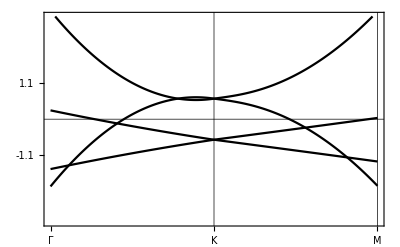

```mathematica
bandplot[path,200,ham,{Subscript[C, 0,1]->0,Subscript[C, 0,2]->0.6,Subscript[C, 1,1]->0.1,Subscript[C, 1,2]->0,Subscript[C, 1,3]->0,Subscript[C, 2,1]->0,Subscript[C, 2,2]->0.13,Subscript[C, 2,3]->0,Subscript[C, 2,4]->0.12,Subscript[C, 2,5]->0,Subscript[C, 2,6]->0,Subscript[C, 2,7]->0},"PlotRange"->{-3,3}]
```